# Assignment 6

## 1.

We find an expression for the range of a projectile fired at an initial velocity v.

```mathematica
it=Solve[vy0*t-1/2*g*t^2==0&&t≠0,t]
```

{{t→(2 vy0)/g}}

```mathematica
vy0=√(v^2-vx0^2);
```

```mathematica
range=vx0*t/.it[[1]][[1]]
```

(2 vx0 √(v^2-vx0^2))/g

```mathematica
frange[x_]:=range/.vx0->x
```

```mathematica
diffrange[x_]:=frange'[x]
```

```mathematica
maxrange=Solve[diffrange[vx0]==0,v]
```

{{v→-√2 vx0},{v→√2 vx0}}

This shows that range is maximized for v = ± √2 v_x_0 ⇒ v_y_0= √(v^2-v_x_0^2)= v_x_0. Since the vertical and horizontal components of the initial velocity are equal, the optimal firing angle is 45° as stated. We now find the velocity components to reach PCC from Caltech (1000m):

```mathematica
g=9.81;
fmaxrange[x_]:=frange[x]/.maxrange[[1]][[1]]/.vx0->x
```

```mathematica
Solve[fmaxrange[vx0]==1000,vx0,Reals]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{vx0→70.0357}}

This gives us that in order to reach PCC from Caltech, we need to have v_x_0= v_y_0=70.03 ms^-1.

## 2.

We set x_0 = y_0 = 0 since we can always do this by a change of coordinates. We also set v = √2 since we only need to concern ourselves with the firing angle. If our previous result is correct, we expect the maximum range to be obtained for v_y_0= 1.

```mathematica
g=9.81;
Manipulate[ParametricPlot[Evaluate[{x[t],y[t]}/.NDSolve[{x''[t]==0,y''[t]==-g,x[0]==0,x'[0]==Sqrt[2-vy0^2],y[0]==0,y'[0]==vy0},{x[t],y[t]},{t,0,1}]],{t,0,0.4},ImageSize->Large,AxesLabel->{"x","y"},PlotRange->{{0,0.3},{0,0.12}}],{{vy0,0,"v_y_0="},0,1.4,Appearance->"Labeled"}]
```

By manipulating the slider for v_y_0 above, we can observe that the maximum range occurs when v_y_0= 1 ⇒ v_y_0= v_x_0 as expected (we use Manipulate rather than superimposing several plots because in this case it gives a clearer picture of the situation).

## 3.

We set the parameters, then simplify the equations with drag and solve them numerically using the firing velocity found in part 1 as initial conditions.

```mathematica
r=0.05;
m=0.5;
ρ=1.3;
g=9.81;
```

```mathematica
rule=NDSolve[{x''[t]==-(ρ*r^2)/(2*m)(y'[t]*Sqrt[x'[t]^2+y'[t]^2]),y''[t]==-g-(ρ*r^2)/(2*m)(x'[t]*Sqrt[x'[t]^2+y'[t]^2]),x[0]==0,x'[0]==70.03,y[0]==0,y'[0]==70.03},{x,y},{t,0,9}]
```

{{x→InterpolatingFunction[{{0., 9.}}, <>],y→InterpolatingFunction[{{0., 9.}}, <>]}}

```mathematica
xx[t_]:=x[t]/.rule[[1]]
yy[t_]:=y[t]/.rule[[1]]
```

```mathematica
impact=FindRoot[yy[t]==0,{t,5}]
```

{t→6.76974}

```mathematica
xx[t]/.impact
```

352.673

This gives us that the grapefruit lands 353m away from Caltech in the direction of PCC if fired with initial velocity components as calculated without accounting for drag.

## 4.

```mathematica
sol=ParametricNDSolve[{x''[t]==-(ρ*r^2)/(2*m)(y'[t]*Sqrt[x'[t]^2+y'[t]^2]),y''[t]==-g-(ρ*r^2)/(2*m)(x'[t]*Sqrt[x'[t]^2+y'[t]^2]),x[0]==0,x'[0]==vx0,y[0]==0,y'[0]==vy0},{x,y},{t,0,50},{vx0,vy0},Method->"StiffnessSwitching"]
```

{x→ParametricFunction[<>],y→ParametricFunction[<>]}

```mathematica
plot1=ParametricPlot[Evaluate[{x[350,360][t],y[350,360][t]}/.sol],{t,0,12},ImageSize->Large,AxesLabel->{"x","y"},PlotRange->{{0,1200},{0,600}},PlotStyle->Blue,PlotLegends->{"v_x_0= 350, v_y_0= 360, v = 502"}];
```

```mathematica
plot2=ParametricPlot[Evaluate[{x[410,410][t],y[410,410][t]}/.sol],{t,0,7.5},ImageSize->Large,AxesLabel->{"x","y"},PlotRange->{{0,1200},{0,600}},PlotStyle->Yellow,PlotLegends->{"v_x_0= 410, v_y_0= 410, v = 580"}];
```

```mathematica
plot3=ParametricPlot[Evaluate[{x[540,530][t],y[540,530][t]}/.sol],{t,0,5},ImageSize->Large,AxesLabel->{"x","y"},PlotRange->{{0,1200},{0,600}},PlotStyle->Green,PlotLegends->{"v_x_0= 540, v_y_0= 530, v = 757"}];
```

```mathematica
plot4=ParametricPlot[Evaluate[{x[345,355][t],y[345,355][t]}/.sol],{t,0,12},ImageSize->Large,AxesLabel->{"x","y"},PlotRange->{{0,1200},{0,600}},PlotStyle->Red,PlotLegends->{"v_x_0= 345, v_y_0= 355, v = 495"}];
```

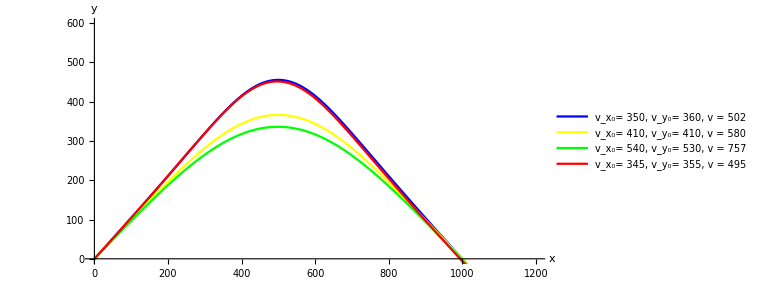

```mathematica
Show[plot1,plot2,plot3,plot4]
```

By considering some trajectories with the required range, we observe that the components that minimize the initial velocity are v_x_0≈ 345, v_y_0≈ 355, giving v ≈ 495 and a firing angle of θ ≈ 0.80_rad. (Here it is more difficult to use Manipulate, because the system becomes stiff beyond a certain value of t different for different initial conditions that might be within impact time of other trajectories, and stiffness causes anomalous behavior in NDSolve and the subsequent plot. We will have to handle this in the next section, but use the superimposed plots for this part as they are more immediately informative when we have two parameters to vary.)

## 5.

```mathematica
r=0.05;
m=0.5;
ρ=1.3;
g=9.81;
soln=ParametricNDSolve[{x''[t]==-(ρ*r^2)/(2*m)(y'[t]*Sqrt[x'[t]^2+y'[t]^2]),y''[t]==-g-(ρ*r^2)/(2*m)(x'[t]*Sqrt[x'[t]^2+y'[t]^2]),x[0]==0,x'[0]==vx0,y[0]==0,y'[0]==vy0,WhenEvent[y[t]<0,"StopIntegration"]},{x,y},{t,0,100},{vx0,vy0},Method->"StiffnessSwitching"]
```

{x→ParametricFunction[<>],y→ParametricFunction[<>]}

```mathematica
yfnt[vx0_,vy0_,t_]:=y[vx0,vy0][t]/.soln
xfnt[vx0_,vy0_,t_]:=x[vx0,vy0][t]/.soln
```

```mathematica
tfninit[vx0_,vy0_]:=t/.FindRoot[yfnt[vx0,vy0,t]==0,{t,3,30}]//Quiet
```

```mathematica
range[vx0_,vy0_]:=xfnt[vx0,vy0,tfninit[vx0,vy0]]
```

```mathematica
range2[v_?NumericQ,θ_?NumericQ]:=range[v*Cos[θ],v*Sin[θ]]
```

```mathematica
initv[x_,θ_]:=Catch[Do[If[x-0.05<range2[v,θ]<x+0.05,Throw[v]],{v,400,800,0.1}]]//Quiet
```

```mathematica
minv[x_]:=Catch[Do[If[initv[x,θ]==initv[x,θ+0.0001],Throw[θ]],{θ,0.7975,0.8100,0.0001}]]
```

```mathematica
{timing,vmin}=Timing[minv[1000]]
```

{41.0894,0.798}

```mathematica
initv[1000,vmin]
```

501.4

We use the range for the optimal firing angle and velocity found by trial and error to define our iteration over a domain for which our functions defined above behave nicely (we can change the parameters of the functions above if we ever need to find the optimal firing angle and velocity for other ranges). Our iterations then give us an optimal firing angle of 0.7980_rad and firing velocity of 501.4 ms^-1, not too far from our guess in part 4. We can observe graphically that the minimum given by our iteration lies in the correct range for θ and v_0.

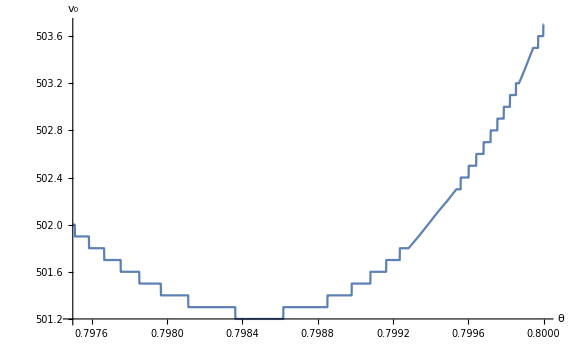

```mathematica
Plot[initv[1000,θ],{θ,0.7975,0.8000},ImageSize->Large,AxesLabel->{"θ","v_0"}]
```